```mathematica
FileExport[data_, filename_?StringQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

```mathematica
SetDirectory[FileNameJoin[{ParentDirectory@NotebookDirectory[], "data"}]]
```

/Users/arsenytokarev/Desktop/CourseWorks/Gas Dynamics/Code/data

```mathematica
NormalRepresentation[data_List]:= Module[
{solution, mesh},
solution = {ToExpression@#⟦1⟧, #⟦2⟧} &/@ data;
For[i =1, i <= Length@solution, ++i,
 solution⟦i,2⟧ = {ToExpression@#⟦1⟧, ToExpression@#⟦2⟧} &/@ solution⟦i,2⟧
];
Return[Sort@solution]
];
```

```mathematica
Plots[data_List]:= ListPlot[#⟦2⟧ &/@ data, PlotRange->All, ImageSize->500, GridLines->Automatic, Ticks->{Table[i, {i, 0, 200, 20}], {0, 1}}]
```

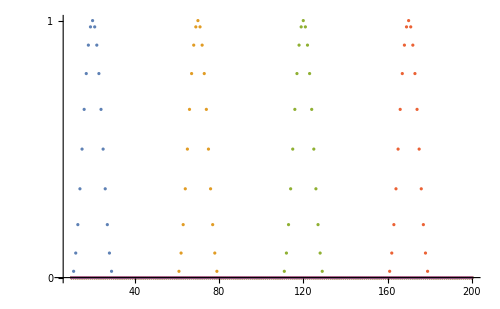

```mathematica
advection = NormalRepresentation@Import["advection.json"] ;
Plots[advection]
```

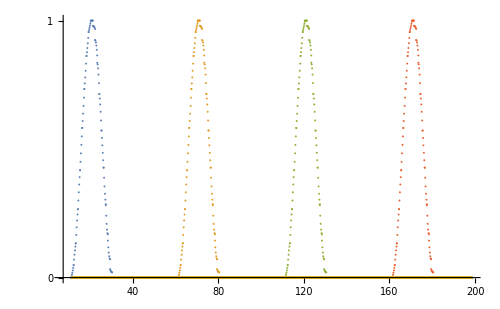

```mathematica
advectionPPM = NormalRepresentation@Import["advectionPPM.json"] ;
Plots[advectionPPM]
```

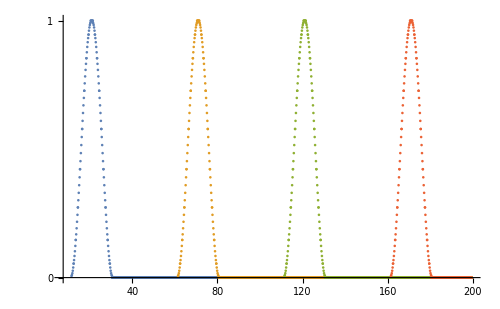

```mathematica
advectionPPML = NormalRepresentation@Import["advectionPPML.json"] ;
Plots[advectionPPML]
```

```mathematica
FileExport[advectionPPM, "advection_ppm.pdf", PDF]
```